```mathematica
M=({{(Cos[ϕ])^2-Za/Zb Sin[ϕ], -I(Za+Zb)Sin[ϕ]Cos[ϕ]}, {-I(1/Za+1/Zb)Sin[ϕ]Cos[ϕ], (Cos[ϕ])^2-Zb/Za(Sin[ϕ])^2}});
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
{{λ1,λ2},{v1,v2}}=Eigensystem[M];
```

```mathematica
P'={v1,v2};
```

```mathematica
P=Transpose[P'];
```

```mathematica
A=MatrixPower[({{λ1, 0}, {0, λ2}}),L];
```

```mathematica
Inverse[P];
```

```mathematica
X= P.A.Inverse[P];
```

```mathematica
Equations={1+r==X[[1,1]]*t+X[[1,2]]*t/ZN,(1-r)/(Z1)==X[[2,1]]*t+X[[2,2]]*t/ZN};
```

```mathematica
Solution=Solve[Equations,{r,t}];
```

```mathematica
Z0=376.31;
Za= Z0/1.75;
Zb=Z0/2.5;
ϕ=1.75*125*10^(-9)*2*Pi/x;
```

```mathematica
Z1=Z0/1;
ZN= Z0/2.5;
```

```mathematica
t=t/.Solution[[1]];
r= r/.Solution[[1]];
```

```mathematica
Plot[Z1/ZN Norm[t]^2/.{L->30},{x,600*10^(-9),1200*10^(-9)}];
List[Z1/ZN Norm[t]^2/.{L->30},{x,600*10^(-9),1200*10^(-9),1*10^(-9)}];
```

```mathematica
R=(ComplexExpand[Abs[r]])^2;
```

```mathematica
R/.{x->600*10^(-9)}
```

0.124893

```mathematica
L=30;
```

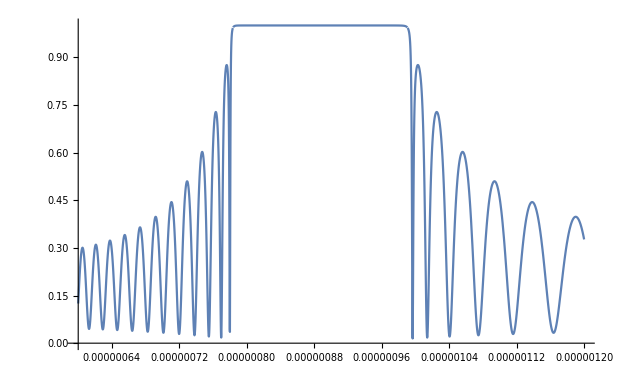

```mathematica
Plot[R,{x,600*10^(-9),1200*10^(-9)}]
```